```mathematica
β[ω_,δ_,t_,ϵ_]:=
β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[14],Join[Table[{i,i-1},{i,Range[2,14,1]}],Table[{i,i+1},{i,Range[1,14,1]}],Table[{2n-1,14-2n+2},{n,4}],Table[{14-2n+2,2n-1},{n,3}]]->t]
```

```mathematica
T1[t_]:=T1[t]=ReplacePart[0*IdentityMatrix[14],Table[{2n,14-2n+1},{n,3}]->t]
```

```mathematica
TT[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,2n},{n,3}]->t]
```

```mathematica
Lead=Table[ToExpression[Import["/home/shardul/PhD_new/PhD/fwi/AGNR/7AGNR/Leads/lead_"<>ToString[X]<>".dat"]],{X,Range[0,3,0.01]}]
```

{{{0.-0.0000823223 ⅈ,-0.573223+0. ⅈ,0.+0.000025 ⅈ,0.25+0. ⅈ,0.-2.8033×10^-13 ⅈ,-0.0732233+0. ⅈ,0.-7.32233×10^-6 ⅈ,0.0732233+0. ⅈ,0.+0.0000146447 ⅈ,-0.176777+0. ⅈ,0.-0.0000323223 ⅈ,0.323223+0. ⅈ,0.+0.0000396447 ⅈ,-0.426777+0. ⅈ},12,{-0.426777+0. ⅈ,12,0.-1035.53 ⅈ}},299,{1}}
 |  |  |  |

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Lead[[ω*100+1]]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
Clear[SR,SL]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=SR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=SL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SL[ω,δ,t,ϵ].TT[t].SR[ω,δ,t,ϵ].TT[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ].TT[t].SL[ω,δ,t,ϵ].TT[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].TT[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:=tr[ω,δ,t,ϵ]=Abs[Tr[gdd[ω,δ,t,ϵ].TT[t].grr[ω,δ,t,ϵ].TT[t]-TT[t].GNON[ω,δ,t,ϵ].TT[t].GNON[ω,δ,t,ϵ]]]
```

```mathematica
tr[0.7,0.0001,1,0]
```

2.

```mathematica
Clear[pris]
```

```mathematica
pris:=pris= Table[tr[ω,0.0001,1,0],{ω,Range[0,3,0.01]}]
```

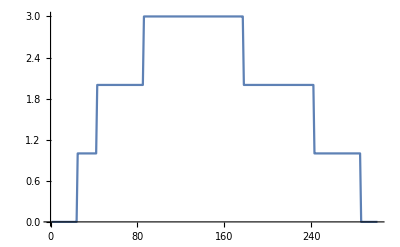

```mathematica
ListLinePlot[pris]
```

```mathematica
list[up_]:=Join[Transpose[Join[{Range[1,100]},{RandomSample[Join[Table[0,100-up],Table[RandomChoice[Range[1,14,1]],up]]]}]]]
```

```mathematica
dist[up_]:=dist[up(*,downleft,upright,downright*)]=Table[list[up(*,downleft,upright,downright*)],5000]
```

```mathematica
Clear[dist]
```

```mathematica
data[ω_,ϵ1_,up_,number_]:=Module[{Tin=T1[1],T=TT[1]},
sl1=Module[{J= SL[ω,0.0001,1,0]},
Do[J=Inverse[IdentityMatrix[14]-Inverse[Module[{κ=β[ω,0.0001,1,0],n= dist[up][[number]][[loc1,2]]},ReplacePart[κ,{{n,n}}->ω+ⅈ*0.0001-ϵ1]]].ConjugateTranspose[T1[1]].J.T1[1]].Inverse[Module[{κ=β[ω,0.0001,1,0],n= dist[up][[number]][[loc1,2]]},ReplacePart[κ,{{n,n}}->ω+ⅈ*0.0001-ϵ1]]],{loc1,100}];
J=J];
Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];final=Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]];final]
```

```mathematica
Clear[input]
```

```mathematica
Clear[f]
```

```mathematica
f1[conc_,num_]:=ParallelTable[{ω,If[data[ω,0.5,conc,num]>tr[ω,0.0001,1,0],tr[ω,0.0001,1,0],data[ω,0.5,conc,num]]},{ω,Range[0,3,0.01]}]
```

```mathematica
input[xyz_]:=input[xyz]= Monitor[Table[f1[xyz,num],{num,50}],num]
```

```mathematica
input[20]
```

{{{0.,1.63212×10^-7},{0.01,2.52255×10^-7},{0.02,2.82308×10^-7},{0.03,2.53951×10^-7},{0.04,1.64717×10^-7},{0.05,8.85338×10^-9},{0.06,2.23185×10^-7},{0.07,3.25045×10^-7},286,{2.94,2.8098×10^-7},{2.95,2.28152×10^-7},{2.96,1.88907×10^-7},{2.97,1.58966×10^-7},{2.98,1.35611×10^-7},{2.99,1.17044×10^-7},{3.,1.02043×10^-7}},48,{1}}
 |  |  |  |

```mathematica
Export["~/Desktop/Thesis/thesis26jun/Images/Chapter3/7agnrtrans.dat",f[42,2]]
```

~/Desktop/Thesis/thesis26jun/Images/Chapter3/7agnrtrans.dat

```mathematica
Monitor[Table[Table[NIntegrate[Interpolation[%58[[conc]][[n]]-x123][x],{x,1.,150.}],{n,50}],{conc,21}],{conc,n}]
```

```mathematica
Table[Around[%61[[x]]],{x,19}]/297.5
```

{0.999999,0.8360.013,0.7300.013,0.6540.016,0.5870.017,0.5360.016,0.4980.017,0.4570.015,0.4250.016,0.3980.016,0.3720.016,0.3500.019,0.3340.019,0.3180.019,0.3000.019,0.2850.017,0.2760.015,0.2680.015,0.2540.019}

```mathematica
inp[onsite_,num_]:=ToExpression[Import["~/PhD_new/PhD/fwi/AGNR/7AGNR/100unitcells/test_onsite_"<>ToString[onsite]<>"_conc_"<>ToString[num]<>"_.dat"]]
```

```mathematica
Table[Table[{num,NIntegrate[Interpolation[ParallelTable[Flatten[inp[onsite,num]][[x]],{x,30,280}]][y],{y,1,140}]/NIntegrate[Interpolation[ParallelTable[pris[[x]],{x,30,280}]][y],{y,1,140}]},{num,Range[5,90,5]}],{onsite,0.05,1,0.1}]
```

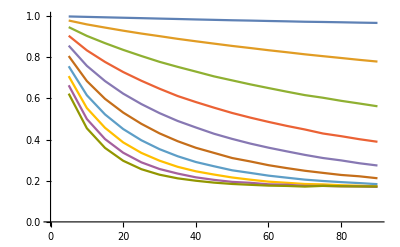

```mathematica
ListPlot[%30,Joined->True]
```

```mathematica
transmission100[x_]:=transmission100[x]=Import["/home/shardul/PhD_new/PhD/fwi/AGNR/7AGNR/100unitcells/resolve/test"<>ToString[x]<>".dat"]
```

```mathematica
misfit100[x_,y_,n_]:=Module[{m5=input[20][[n]]},
ρ1:= Table[{ξ,
Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]-transmission100[ξ][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]},{ξ,Range[1,100,2]}]; 
whysamemistake=Transpose[Join[{Range[1,100,10]},{ρ1}]];ρ1(*whysamemistake*)(*whysamemistake[[Position[whysamemistake,Min[whysamemistake]][[1,1]]]][[1]]*)]
```

```mathematica
misfit100[0.5,2.1,1]
```

{{1,0.0131804},{11,0.00246168},{21,0.00116441},{31,0.00193766},{41,0.00325843},{51,0.00469827},{61,0.00603046},{71,0.00720787},{81,0.00824182},{91,0.00911032}}

```mathematica
Export["~/Desktop/Thesis/thesis26jun/Images/Appendix/misfit_10.dat",%31]
```

~/Desktop/Thesis/thesis26jun/Images/Appendix/misfit_10.dat

```mathematica
Export["~/Desktop/Thesis/thesis26jun/Images/Appendix/misfit_100.dat",%33]
```

~/Desktop/Thesis/thesis26jun/Images/Appendix/misfit_100.dat

```mathematica
misfit100[0.5,2.1,1]
```

{{1,0.0131804},{3,0.00896297},{5,0.00631527},{7,0.00453387},{9,0.00330213},{11,0.00246168},{13,0.00188534},{15,0.00150786},{17,0.0012948},{19,0.00118611},{21,0.00116441},{23,0.00122519},{25,0.0013484},{27,0.00151795},{29,0.00171337},{31,0.00193766},{33,0.00215675},{35,0.00244383},{37,0.00269768},{39,0.0029869},{41,0.00325843},{43,0.00355577},{45,0.00384431},{47,0.00413701},{49,0.00440423},{51,0.00469827},{53,0.00497934},{55,0.00525232},{57,0.00552271},{59,0.00574758},{61,0.00603046},{63,0.00627753},{65,0.00652435},{67,0.00677183},{69,0.00698855},{71,0.00720787},{73,0.0074314},{75,0.00762485},{77,0.00784517},{79,0.00802786},{81,0.00824182},{83,0.00840693},{85,0.00859499},{87,0.00875633},{89,0.00891435},{91,0.00911032},{93,0.00926558},{95,0.00940066},{97,0.00951225},{99,0.0096647}}

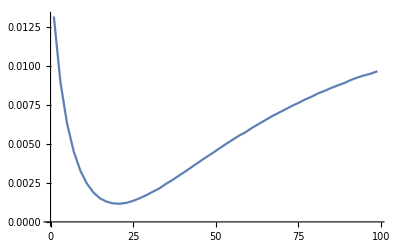

```mathematica
ListPlot[%33,Joined->True]
```

```mathematica
abc=Table[misfit100[0.5,2.7,n],{n,50}]
```

Part::partd: Part specification input⟦1⟧ is longer than depth of object.

Part::take: Cannot take positions 1 through 300 in input⟦1⟧.

Part::partd: Part specification input⟦1⟧ is longer than depth of object.

Part::take: Cannot take positions 1 through 300 in input⟦1⟧.

Transpose::nmtx: The first two levels of {input⟦1⟧,{(-2.8×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,(-2.78688×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,(-2.81426×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,(-2.86149×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,(-2.91921×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,(-2.99702×10^-7+input⟦1⟧⟦«1»⟧)^2,(-3.104×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,(-3.236×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,(-3.39098×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,(-3.60208×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,«290»}} cannot be transposed.

Interpolation::innd: First argument in Transpose[{input⟦1⟧,{(-2.8×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,(-2.78688×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,(-2.81426×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,(-2.86149×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,(-2.91921×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,(-2.99702×10^-7+«1»)^2,(-3.104×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,(-3.236×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,(-3.39098×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,(-3.60208×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,«290»}}] does not contain a list of data and coordinates.

Part::take: Cannot take positions 1 through 300 in input⟦1⟧.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partd: Part specification input⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {input⟦1⟧,{(-2.78025×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,(-2.66272×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,(-2.68557×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,(-2.72755×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,(-2.80017×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,(-2.8664×10^-7+«1»)^2,(-2.99137×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,(-3.10945×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,(-3.24814×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,(-3.44426×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,«290»}} cannot be transposed.

Interpolation::innd: First argument in Transpose[{input⟦1⟧,{(-2.78025×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,(-2.66272×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,(-2.68557×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,(-2.72755×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,(-2.80017×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,(-2.8664×10^-7+«1»)^2,(-2.99137×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,(-3.10945×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,(-3.24814×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,(-3.44426×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,«290»}}] does not contain a list of data and coordinates.

Transpose::nmtx: The first two levels of {input⟦1⟧,{(-2.72136×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,(-2.57819×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,(-2.59784×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,(-2.6677×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,(-2.72295×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,(-2.81845×10^-7+input⟦1⟧⟦«1»⟧)^2,(-2.92443×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,(-3.05773×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,(-3.188×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,(-3.3809×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,«290»}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Interpolation::innd: First argument in Transpose[{input⟦1⟧,{(-2.72136×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,(-2.57819×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,(-2.59784×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,(-2.6677×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,(-2.72295×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,(-2.81845×10^-7+«1»⟦«1»⟧)^2,(-2.92443×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,(-3.05773×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,(-3.188×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,(-3.3809×10^-7+input⟦1⟧⟦1;;300,2⟧)^2,«290»}}] does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

$Aborted

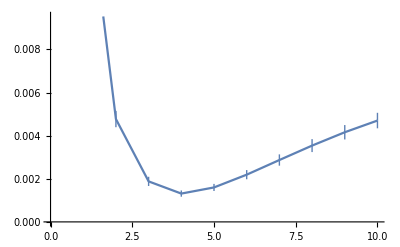

```mathematica
Table[Around[Table[abc[[n]][[x]],{n,100}]],{x,10}]//ListLinePlot
```

```mathematica
Export["~/Desktop/Thesis/thesis26jun/Images/Chapter3/cnt_error.dat",Table[{x,Mean[Table[abc[[n]][[x]],{n,100}]],StandardDeviation[Table[abc[[n]][[x]],{n,100}]]},{x,10}]]
```

~/Desktop/Thesis/thesis26jun/Images/Chapter3/cnt_error.dat

```mathematica
misfit100[0,1.5,2]//ListLinePlot
```

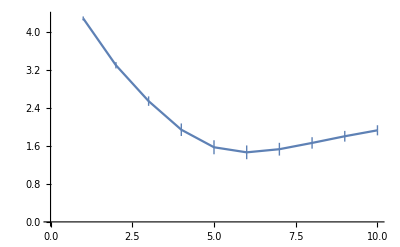

```mathematica
ListLinePlot[Table[{x,Around[Table[%109[[n]][[x]],{n,100}]]},{x,10}]]
```

```mathematica
Table[{x-1,Mean[Table[%61[[n]][[x]],{n,150}]],StandardDeviation[Table[%61[[n]][[x]],{n,150}]]},{x,10}]
```

{{0,0.014524,0.000824502},{1,0.00413204,0.000426037},{2,0.00157497,0.000230529},{3,0.00106628,0.000155177},{4,0.0013275,0.000183693},{5,0.00188282,0.000242432},{6,0.00252367,0.000297258},{7,0.00316871,0.000344347},{8,0.00376552,0.000384089},{9,0.00429058,0.000415184}}

```mathematica
Clear[ca]
```

```mathematica
ca[x_]:=Import["~/PhD_new/PhD/fwi/AGNR/7AGNR/100unitcells/resolve/test"<>ToString[x]<>".dat"]
```

```mathematica
Table[Interpolation[Table[{x,ca[x][[e]][[2]]},{x,Range[1,100,2]}]],{e,10,150,10}]
```

```mathematica
Interpolation[Table[{x,ca[x][[121]][[2]]/3},{x,Range[1,100,2]}]]
```

InterpolatingFunction[…]

```mathematica
Module[{abc=Interpolation[Table[{x,ca[x][[121]][[2]]/3},{x,Range[1,100,2]}]]},Join[{{0,1}},Table[{x,abc[x]},{x,1.,99.}]]]
```

```mathematica
Table[Fit[Module[{abc=Interpolation[Table[{x/100,ca[x][[y]][[2]]/3},{x,Range[1,100,2]}]]},Join[{{0,1}},Table[{x,abc[x]},{x,0.01,0.99}]]],{1,x,x*x,ⅇ^x},x],{y,90,110}]
```

{0.502572+0.497428 ⅇ^x-2.38134 x-238.134 x^2,0.502565+0.497435 ⅇ^x-2.11574 x-211.574 x^2,0.50256+0.49744 ⅇ^x-1.88778 x-188.778 x^2,0.502556+0.497444 ⅇ^x-1.72546 x-172.546 x^2,0.502553+0.497447 ⅇ^x-1.63209 x-163.209 x^2,0.502549+0.497451 ⅇ^x-1.47297 x-147.297 x^2,0.502548+0.497452 ⅇ^x-1.41056 x-141.056 x^2,0.502546+0.497454 ⅇ^x-1.34123 x-134.123 x^2,0.502544+0.497456 ⅇ^x-1.26703 x-126.703 x^2,0.502542+0.497458 ⅇ^x-1.17046 x-117.046 x^2,0.502541+0.497459 ⅇ^x-1.14207 x-114.207 x^2,0.50254+0.49746 ⅇ^x-1.101 x-110.1 x^2,0.50254+0.49746 ⅇ^x-1.09194 x-109.194 x^2,0.502542+0.497458 ⅇ^x-1.18591 x-118.591 x^2,0.502551+0.497449 ⅇ^x-1.5377 x-153.77 x^2,0.502574+0.497426 ⅇ^x-2.47549 x-247.549 x^2,0.502646+0.497354 ⅇ^x-5.34435 x-534.435 x^2,0.502779+0.497221 ⅇ^x-10.6481 x-1064.81 x^2,0.502771+0.497229 ⅇ^x-10.3572 x-1035.72 x^2,0.502691+0.497309 ⅇ^x-7.15437 x-715.437 x^2,0.502642+0.497358 ⅇ^x-5.20096 x-520.096 x^2}

```mathematica
Plot[x/Exp[x],{x,0,100}]
```

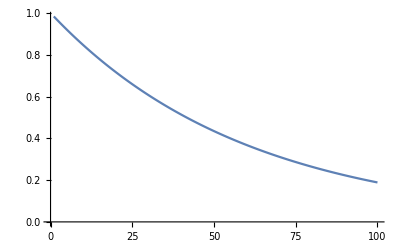

```mathematica
Table[Exp[-n/60],{n,100}]//ListLinePlot
```

```mathematica
Join
```

```mathematica
Clear[f2]
```

```mathematica
Dimensions[pris]
```

{301}

```mathematica
pris[[114]]
```

3.

```mathematica
f2[ω_]:=f2[ω]=Transpose[Join[{Range[1,81,2]},{Join[{pris[[ω*100+1]]},Table[transmission100[a][[Round[ω*100+1],2]],{a,Range[3,81,2]}]]}]]
```

```mathematica
f2[1.25]
```

{{1,3.},{3,2.71574},{5,2.55128},{7,2.40773},{9,2.27367},{11,2.15699},{13,2.04217},{15,1.92917},{17,1.84212},{19,1.75648},{21,1.6739},{23,1.59552},{25,1.54122},{27,1.46984},{29,1.41055},{31,1.35257},{33,1.30306},{35,1.23954},{37,1.2017},{39,1.15987},{41,1.11498},{43,1.07603},{45,1.04375},{47,0.984018},{49,0.958481},{51,0.921875},{53,0.884112},{55,0.860573},{57,0.829957},{59,0.810185},{61,0.780518},{63,0.771406},{65,0.72384},{67,0.702651},{69,0.680195},{71,0.672328},{73,0.656859},{75,0.642463},{77,0.624145},{79,0.608991},{81,0.583469}}

```mathematica
Export["~/Desktop/Thesis/thesis26jun/Images/Chapter3/beta_energy.dat",Table[{ω,Abs[f2[ω][[1+1]]-f2[ω][[1]]]},{ω,Range[0,3,0.01]}]]
```

~/Desktop/Thesis/thesis26jun/Images/Chapter3/beta_energy.dat

```mathematica
Export["~/Desktop/Thesis/thesis26jun/Images/Chapter3/beta_5_7agnr.dat",Transpose[Join[{N[Range[1,81,2]/14]},{f2[1.5]}]]]
```

~/Desktop/Thesis/thesis26jun/Images/Chapter3/beta_5_7agnr.dat

```mathematica
f2[1][[Round[71/2]]]
```

{71,1.2147}

```mathematica
Clear[β2]
```

```mathematica
β2[ω_,conc_]:=β2[ω,conc]=Abs[f2[ω][[(*Round[conc/2]*)1,2]]-f2[ω][[2,2]]]
```

```mathematica
β2[1,2]
```

0.143221

```mathematica
β2[1.2,11]
```

0.125905

```mathematica
Monitor[Table[input[conc],{conc,Range[1,70,10]}],{conc}]
```

{{1},5,{{{0.,2.8×10^-7},{0.01,2.8081×10^-7},{0.02,2.83264×10^-7},295,{2.98,1.35611×10^-7},{2.99,1.17044×10^-7},{3.,1.02043×10^-7}},48,{1}}}
 |  |  |  |

```mathematica
Table[Table[β2[ω,Z],{ω,Range[0,3,0.01]}],{Z,1,60,10}]
```

{1}
 |  |  |  |

```mathematica
n[conc_,num_,x_,y_]:= NIntegrate[Interpolation[Table[{ω,β2[ω,2]*(-input[conc][[num]][[ω*100+1,2]]+pris[[ω*100+1]])},{ω,Range[0,2,0.01]}]][v],{v,0,2}]/NIntegrate[Interpolation[Table[{ω,β2[ω,2]*β2[ω,2]},{ω,Range[0,2,0.01]}]][p],{p,0,2}]
```

```mathematica
input[3]
```

{{{0.,2.8×10^-7},{0.01,2.8081×10^-7},{0.02,2.83264×10^-7},{0.03,2.87437×10^-7},294,{2.98,1.35611×10^-7},{2.99,1.17044×10^-7},{3.,1.02043×10^-7}},48,{1}}
 |  |  |  |

```mathematica
Table[β2[ω,2],{ω,Range[0.1,3,0.01]}]
```

```mathematica
Table[{10*y+1,Abs[Around[Table[n[10*y+1,x,0.9,1.5],{x,50}]]]},{y,6}]
```

{{11,2.170.12},{21,2.870.11},{31,3.240.10},{41,3.530.11},{51,3.720.11},{61,3.910.09}}

```mathematica
Abs[Around[Table[Abs[n[7,num,0.9,1.5]],{num,50}]]]
```

$Aborted

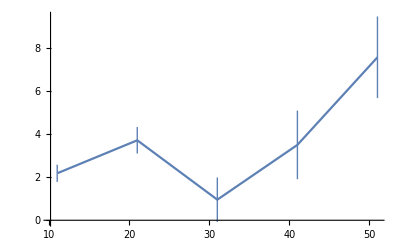

```mathematica
Table[{z,Abs[Around[Table[Abs[n[5,num,0.9,1.5]],{num,50}]]-z]},{z,Range[11,60,10]}]//ListLinePlot
```